## Convert Covid-19 Cases

```mathematica
path0=NotebookDirectory[];
coviddata=Import[path0<>"covid.csv","CSV"];
days=DayCount[coviddata[[2,4]],coviddata[[-1,4]]]
cases=coviddata[[2;;,6]];
death=coviddata[[2;;,9]];
```

620

```mathematica
avgcase=Table[t1=Round[5.3*i];t2=Round[5.3*(i+1)];Round[Plus@@cases[[t1+1;;t2]]],{i,0,Floor[days/5.3]}];
avgdeath=Table[t1=Round[5.3*i];t2=Round[5.3*(i+1)];Round[Plus@@death[[t1+1;;t2]]],{i,0,Floor[days/5.3]}];
Export[path0<>"cases.csv",{avgcase},"CSV"];
Export[path0<>"casesD.csv",{avgdeath*1/0.0037},"CSV"];
```

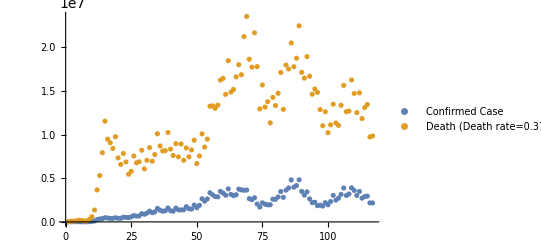

```mathematica
ListPlot[{avgcase,1/0.0037*avgdeath},PlotLegends->{"Confirmed Case","Death (Death rate=0.37%)"}]
```

## Plot TDeltaT

```mathematica
(*Functions*)
TDeltaT[lineage_,n_]:=
Module[{t0},
t0=lineage[[1]];
{t0,lineage[[n+1]]}
]
getDeltaT[lineagelist_,n_]:=TDeltaT[#,n]&/@lineagelist

path0=NotebookDirectory[];
k = {1,2,3};
lineage=Import[path0<>"data/N2.0E+07K"<>ToString[#]<>"M1E-05A.out","CSV"]&/@k;
(*lineageA=Import[path0<>"data/K"<>ToString[#]<>"M5E-05A.out","CSV"]&/@k;*)
Mean/@lineage[[1;;3,;;,1]]//N(*T*)
Mean/@lineage[[1;;3,;;,2]]//N(*DeltaT*)
Dimensions/@lineage
```

{1.,23.334,109.923}

{4.163,4.716,7.148}

{{1000},{1000},{1000}}

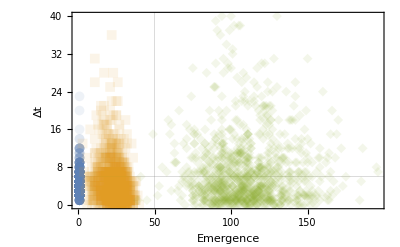

```mathematica
(*1st VOC: 2020Sep, 2nd VOC: 2020OCT*)
actual={{50,6}};

DataTDeltaT=getDeltaT[#,1]&/@lineage;
ListPlot[DataTDeltaT,PlotRange->All,PlotMarkers->{Automatic, Medium},Frame->True,FrameLabel->{"Emergence","Δt"},PlotStyle->Opacity[0.1],GridLines->{{{actual[[1,1]],{Thick,Red}}},{{actual[[1,2]],{Thick,Red}}}}]
```

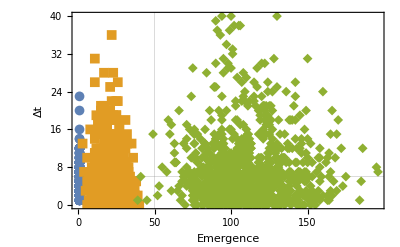

-Graphics3D-

```mathematica
(*1st VOC: 2020Sep, 2nd VOC: 2020OCT*)
actual={{50,6}};

DataTDeltaT=getDeltaT[#,1]&/@lineage;
ListPlot[DataTDeltaT,PlotRange->All,PlotMarkers->{Automatic, Medium},Frame->True,FrameLabel->{"Emergence","Δt"},GridLines->{{{actual[[1,1]],{Thick,Red}}},{{actual[[1,2]],{Thick,Red}}}}]

Histogram3D[Append[DataTDeltaT,actual],Automatic,"Probability",ChartLabels->Placed[{"k=1","k=2","k=3","Real"},Above,"Framed"]]
```